# Toy Model - 3D

```mathematica
Clear["Global`*"]
Ω ={
  {-s, δ, 0},
  {δ, 0, 0},
  {0, 0, 0}
};
Slack = {
{0,0,β},
{1,-β,δ},
{1,0,0}
};
```

```mathematica
(*Define matrix of RHS A*)
LinApp = Slack+(Ω/ε);
Print["Resulting linear application :", LinApp //MatrixForm] 
vars = {ϕ[t], ψ[t], A[t]};
(* Construct ODE system *)
full = (LinApp.vars);
initCond = {ϕ[0] == ϕ0, ψ[0]== ψ0, A[0] == A0};
eqns = Join[
  Thread[D[vars, t] == full],
  initCond
];
Print["Full system field :", eqns //MatrixForm] 
(* Find rows with 1/ε dependece*)
fastRows = Select[Range[Length[full]], ! FreeQ[full[[#]], 1/ε] &];
slowRows = Select[Range[Length[full]], FreeQ[full[[#]], 1/ε] &];
(*Extract these fast equations equations *)
fastEqs = full[[fastRows]];
fastVars = vars[[fastRows]];
slowEqs = Delete[full, List /@ fastRows];
slowVars = vars[[slowRows]];
(* Remove initial conditions for fast variables *)
reducedICs = Select[initCond, FreeQ[#, Alternatives @@ fastVars[[All, 0]]] &];
(*Take ε -> 0 limit to get algebraic constraint *)
algebraicEqs = FullSimplify[Map[# * ε &, fastEqs]];
algebraicEqs = algebraicEqs /. ε -> 0;
(*Solve each fast equation for its associated fast variable *)
criticalManifold = 
  DeleteMissing[
    Table[
      Module[{eq = algebraicEqs[[i]], candidates, sol},
        candidates = Select[vars, ! FreeQ[eq, #] &];
        If[candidates === {}, 
          Missing["NoFastVariableFound"], 
          sol = Quiet@Solve[eq == 0, candidates[[1]]];
          If[sol === {} || ! MatchQ[sol[[1]], _Rule | {__Rule}], 
            Missing["SolveFailed"], 
            sol[[1]]
          ]
        ]
      ],
      {i, Length[algebraicEqs]}
    ]
] //Flatten // FullSimplify;
Print["Critical manifold expression(s):", criticalManifold //MatrixForm ]
```

Resulting linear application :(-s/ε | δ/ε | β
1+δ/ε | -β | δ
1 | 0 | 0)

Full system field :(ϕ'[t]==β A[t]-(s ϕ[t])/ε+(δ ψ[t])/ε
ψ'[t]==δ A[t]+(1+δ/ε) ϕ[t]-β ψ[t]
A'[t]==ϕ[t]
ϕ[0]==ϕ0
ψ[0]==ψ0
A[0]==A0)

Critical manifold expression(s):(ϕ[t]→(δ ψ[t])/s
ϕ[t]→0)

```mathematica
(*Normal hyperbolicity of the critical manifold*)
FastJacobian = D[algebraicEqs,{fastVars}];
Print["Normal hyperbolicity eigenvalues :", Eigenvalues[FastJacobian] ]
(*Reduced system with critical manifold*)
reducedSystem = Join[
  Thread[D[slowVars, t] == slowEqs],
  reducedICs
];
Print["Slow vector field :", reducedSystem//MatrixForm]
```

Normal hyperbolicity eigenvalues :{1/2 (-s-√(s^2+4 δ^2)),1/2 (-s+√(s^2+4 δ^2))}

Slow vector field :(A'[t]==ϕ[t]
A[0]==A0)

```mathematica
NumRep = {
β -> 0.1,
ε -> 0.1,
s -> 0.08,
δ -> 0.01,
ϕ0 -> 0.1,
ψ0 -> 0.1,
A0 -> 0.31
};
```

Numerical integration for the full system

```mathematica
(* Solve the system *)
sol = DSolve[eqns, vars, t];
Eigenvalues[LinApp] /. NumRep;
ϕsol[t_] = ϕ[t] /. sol[[1]] /. NumRep;
ψsol[t_] = ψ[t] /. sol[[1]] /. NumRep;
Asol[t_] = A[t] /. sol[[1]] /. NumRep;
(*Numerical integration of the slow flow*)
solutionSlow = DSolve[reducedSystem, slowVars, t];
slowFunctions = Table[
  Module[{baseSymbol = Head[slowVar], newSym},
    newSym = Symbol[SymbolName[baseSymbol] <> "Slow"];
    newSym[t_] = slowVar /. solutionSlow[[1]] /. NumRep;
    newSym  (* RETURN THE SYMBOL, NOT THE ASSIGNMENT RESULT *)
  ],
  {slowVar, slowVars}
];
```

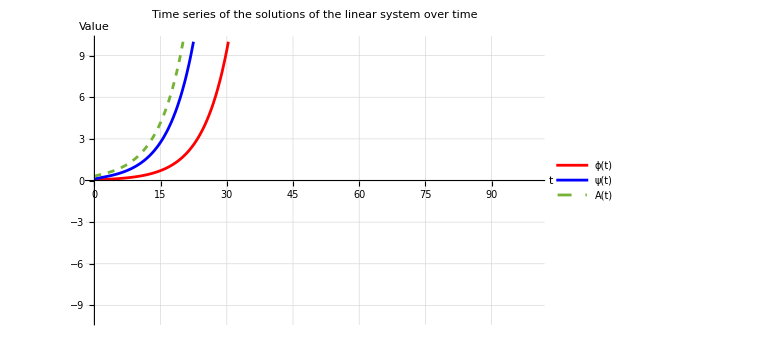

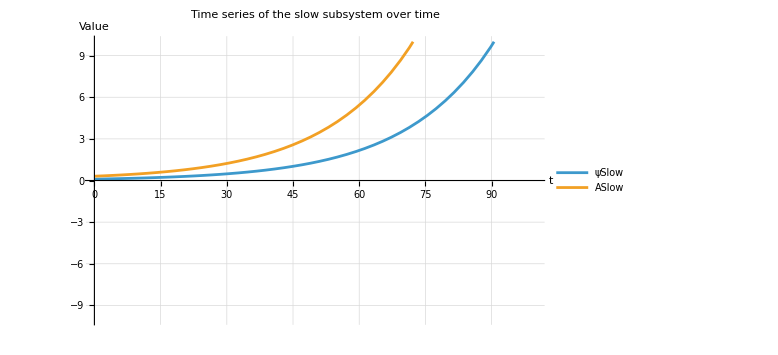

```mathematica
(*Plot full dynamics*)
Plot[
  {ϕsol[t], ψsol[t], Asol[t]},
  {t, 0, 100},
  PlotLegends -> {"ϕ(t)","ψ(t)","A(t)"},
  PlotStyle -> {Red, Blue, Dashed},
  PlotRange -> {-10,10},
  AxesLabel -> {"t", "Value"},
  GridLines -> Automatic,
  ImageSize -> Large,
  PlotLabel -> "Time series of the solutions of the linear system over time"
]
(*Plot slot dynamics*)
Plot[
  Evaluate[Through[slowFunctions[t]]], 
  {t, 0, 100},
  PlotLegends -> slowFunctions, 
  PlotRange -> {-10,10},
  AxesLabel -> {"t", "Value"},
  GridLines -> Automatic,
  ImageSize -> Large,
  PlotLabel -> "Time series of the slow subsystem over time"
]
```